## Modello originale

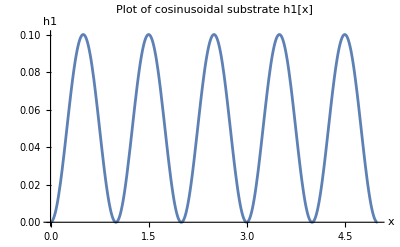

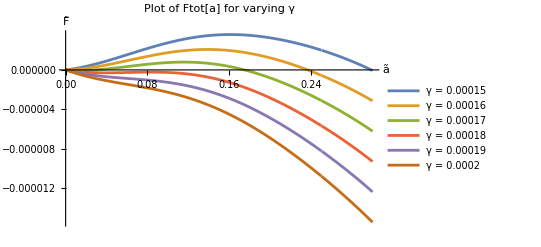

-Graphics3D-

```mathematica
h0=0.1; (*normalized wave amplitude*)
λ=1; (*wavelength*)
s=0.1; (*normalized biolayer thickness*)

h1[x_]:=h0/2*(1-Cos[2 π x/λ]);

Plot[h1[x],{x,0,5},PlotRange->All,AxesLabel->{"x","h1"},PlotLabel->"Plot of cosinusoidal substrate h1[x]"]

Ftot[a_,γ_]:=-(γ *EllipticE[2 π a,-h0^2 π^2])/(2 π)+1/12 π^2 (π^2 a+1/4 π Sin[4 π a]+Sin[2 π a]^2/(1-2 a)) h0^2 s^3+((EllipticE[2 π a,-h0^2 π^2]-2 π a)^2 s)/(4 π^2);

gammas=Range[1.5*10^-4,2*10^-4,1*10^-5];

Plot[Evaluate[Table[Ftot[a,γ],{γ,gammas}]],{a,0,0.3},PlotRange->All,AxesLabel->{OverTilde[a],OverTilde[F]},PlotLegends->("γ = "<>ToString[#]&/@gammas),PlotLabel->"Plot of Ftot[a] for varying γ"]

(*Creazione del grafico 3D*)
data=Flatten[Table[{a,gamma,Ftot[a,gamma]},{a,0,0.3,0.01},{gamma,gammas}],1];

ListPlot3D[data,AxesLabel->{"a","γ","Ftot"},ColorFunction->"Rainbow",InterpolationOrder->3,PlotRange->All,PlotLabel->"3D plot of Ftot[a, γ]"]
```

## Modello serie

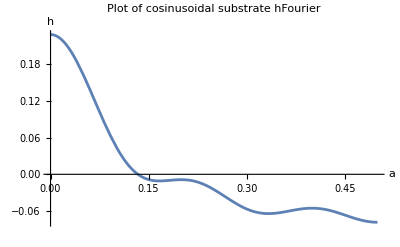

{0.1,0.05,0.0333333,0.025,0.02}

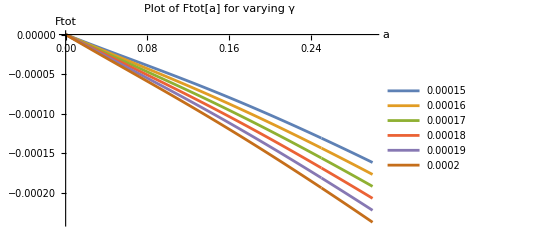

-Graphics3D-

Import::nfurl: Unable to retrieve data from https://raw.githubusercontent.com/francescovissicchio/biomaterials-artificial_organs/master/extract2.txt. Consult Internal`$LastInternalFailure for potential information.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Fourier::fftl: Argument $Failed⟦1⟧ is not a non-empty list or rectangular array of numeric quantities.

```mathematica
(*Parametri del modello con valori fisicamente ragionevoli*)
n=5; (*Numero di componenti della serie di Fourier*)
h[i_]:=0.1/i; (*Ampiezza dell'i-esima componente normalizzata*)
lambda[i_]:=1/i; (*Lunghezza d'onda dell'i-esima componente*)
s=0.1; (*Spessore della membrana cellulare normalizzata*)


(*Serie di Fourier per il profilo del substrato*)
hFourier[a_]:=Sum[h[i]*Cos[2*Pi*a/lambda[i]],{i,1,n}];

Plot[hFourier[a],{a,0,0.5},PlotRange->All,AxesLabel->{"a","h"},PlotLabel->"Plot of cosinusoidal substrate hFourier"]

(*Creazione del vettore dei coefficienti h[i]*)
hCoefficients=Table[h[i],{i,1,n}];

(*Visualizzazione del vettore dei coefficienti*)
hCoefficients

(*Energia totale di adesione*)
Ftot[a_,gamma_]:=Sum[-((gamma*EllipticE[2*Pi*a,-hCoefficients[i]^2*Pi^2])/(2*Pi))+(Pi^2/12)*(Pi^2*a+(Pi/4)*Sin[4*Pi*a]+Sin[2*Pi*a]^2/(1-2*a))*hCoefficients[i]^2*s^3+((EllipticE[2*Pi*a,-hCoefficients[i]^2*Pi^2]-2*Pi*a)^2*s)/(4*Pi^2),{i,1,n}];

Ftot[a_,gamma_]:=Sum[-(gamma *EllipticE[2 π a,-h[i]^2 π^2])/(2 π)+1/12 π^2 (π^2 a+1/4 π Sin[4 π a]+Sin[2 π a]^2/(1-2 a)) h[i]^2 s^3+((EllipticE[2 π a,-h[i]^2 π^2]-2 π a)^2 s)/(4 π^2),{i,1,n}];

(*Gamma range come nel paper*)
gammas=Range[1.5*10^-4,2*10^-4,1*10^-5];
data=Table[{a,gamma,Ftot[a,gamma]},{a,0,0.3,0.01},{gamma,gammas}];

(*Creazione del grafico 2D*)
Plot[Evaluate[Table[Ftot[a,gamma],{gamma,gammas}]],{a,0,0.3},PlotRange->All,AxesLabel->{"a","Ftot"},PlotLegends->Placed[LineLegend[gammas,LegendMarkerSize->8],{0.8,0.5}],PlotLabel->"Plot of Ftot[a] for varying γ"]

(*Creazione del grafico 3D*)
ListPlot3D[Flatten[data,1],AxesLabel->{"a","γ","Ftot"},ColorFunction->"Rainbow",InterpolationOrder->3,PlotRange->All]
```

## Modello con trasformata

-Graphics3D-

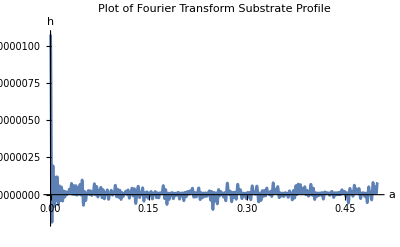

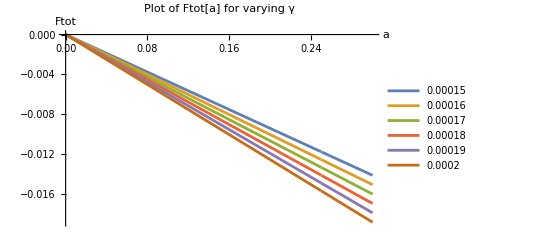

-Graphics3D-

```mathematica
(*Importare i dati*)
data=Import["https://raw.githubusercontent.com/francescovissicchio/biomaterials-artificial_organs/main/extract2.txt","Table"];
ListPlot3D[data]

(*Estrarre la prima riga della matrice*)
coefficients=data[[1]];

(*Calcolare la trasformata di Fourier*)
fourierTransform=Fourier[coefficients];

(*Parametri del modello con valori fisicamente ragionevoli*)
s=0.1; (*Spessore della membrana cellulare normalizzata*)

(*Funzione per il profilo del substrato utilizzando la trasformata di Fourier*)
hFourier[a_]:=Sum[Abs[fourierTransform[[i]]]*Cos[2*Pi*(i-1)*a],{i,1,Length[fourierTransform]}];

(*Visualizzazione del profilo del substrato*)
Plot[hFourier[a],{a,0,0.5},PlotRange->All,AxesLabel->{"a","h"},PlotLabel->"Plot of Fourier Transform Substrate Profile"]

(*Energia totale di adesione*)
Ftot[a_,gamma_]:=Sum[-((gamma*EllipticE[2*Pi*a,-Abs[fourierTransform[[i]]]^2*Pi^2])/(2*Pi))+(Pi^2/12)*(Pi^2*a+(Pi/4)*Sin[4*Pi*a]+Sin[2*Pi*a]^2/(1-2*a))*Abs[fourierTransform[[i]]]^2*s^3+((EllipticE[2*Pi*a,-Abs[fourierTransform[[i]]]^2*Pi^2]-2*Pi*a)^2*s)/(4*Pi^2),{i,1,Length[fourierTransform]}];

(*Gamma range come nel paper*)
gammas=Range[1.5*10^-4,2*10^-4,1*10^-5];
dataPlot=Table[{a,gamma,Ftot[a,gamma]},{a,0,0.3,0.01},{gamma,gammas}];

(*Creazione del grafico 2D*)
Plot[Evaluate[Table[Ftot[a,gamma],{gamma,gammas}]],{a,0,0.3},PlotRange->All,AxesLabel->{"a","Ftot"},PlotLegends->Placed[LineLegend[gammas,LegendMarkerSize->8],{0.8,0.5}],PlotLabel->"Plot of Ftot[a] for varying γ"]

(*Creazione del grafico 3D*)
ListPlot3D[Flatten[dataPlot,1],AxesLabel->{"a","γ","Ftot"},ColorFunction->"Rainbow",InterpolationOrder->3,PlotRange->All]
```